# Bernstein-Vazirani Algorithm

Episode 29. Deutsch-Jozsa Algorithm

Episode 30. Bernstein-Vazirani Algorithm

Episode 31. Simon’s Algorithm

## Statement of the Problem

Suppose that we are given a binary function f:{0,1}^n→{0,1}, the value of which is determined by a secret string s of n bits

f:x↦x·s   (mod 2).

-Graphics-

The Bernstein-Vazirani problem finds the secret bit string s by making queries to the oracle f.

Classically, one needs n queries to the function f to infer the secret string s.

## Quantum Implementation

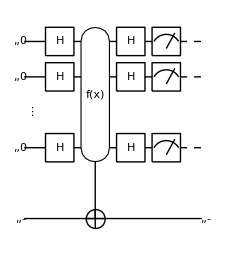

Figure 1. A quantum circuit for the Deutsch-Jozsa algorithm.

The first set of Hadamard gates:

0↦1/2^(n/2)Σ_(x=0)^(2^n-1)x

The quantum oracle:

1/2^(n/2)Σ_(x=0)^(2^n-1)x↦1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(f(x))=1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(x·s) ,

where x·y denotes the bitwise inner product

x·y:=x_1 y_1+x_2 y_2+⋯+x_n y_n  (mod 2),

The second set of Hadamard gates:

1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(x·s)→1/2^(n/2)Σ_(y=0)^(2^n-1)y(Σ_(x=0)^(2^n-1)(-1))^(x·s+x·y)=1/2^(n/2)Σ_(y=0)^(2^n-1)y(Σ_(x=0)^(2^n-1)(-1))^(x·(s⊕y))=s

## Example

Throughout this example, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S,T]
```

Consider a secrete string of bits. The task is to find the secrete string.

```mathematica
string={0,1};
```

In the Bernstein-Vazirani algorithm, the value of the classical oracle f is determined by the given secrete string.

```mathematica
Clear[f];
f[x_List]:={Mod[x.string,2]}
```

For example, f[{1,1}]=0·1 + 1·1=1.

```mathematica
f[{1,1}]
```

Construct a quantum circuit of the Bernstein-Vazirani algorithm. The final Hadamard gate on the target qubit is not necessary, and we put it here to make the output state more readable.

```mathematica
qc=QuantumCircuit[
Ket[S@{1,2}->0,T@{1}->1],
{S[{1,2},6],T[{1},6]},
Oracle[f,S@{1,2},T@{1}],
{S[{1,2},6],T[{1},6]},
Measurement[S[{1,2},3]],
"Invisible"->S@{2.5}
]
```

```mathematica
out=Elaborate[qc];
ProductForm[out,{S@{1,2},T@{1}}]
```

Here is the secrete string successfully retrieved.

```mathematica
answer=out[S@{1,2}]
```

## Summary

### Keywords

Oracle

Decision making

Bernstein-Vazirani problem

### Functions

Oracle

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Bernstein-Vazirani Algorithm